```mathematica
Logistic model
```

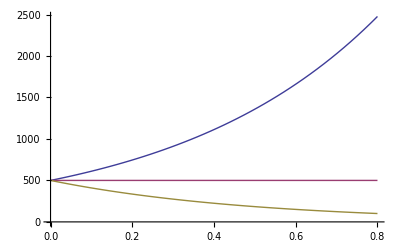

```mathematica
Plot[Evaluate[x[t]/.DSolve[{x'[t]==r x[t],x[0]==a},x,t]/.{{a->500,r-> 2},{a->500,r-> 0},{a->500,r-> -2}}],
{t,0,0.8}]
```

```mathematica
sol= DSolve[{y'[x] ==r y[x](1-y[x]/K),y[0]==a},y,x]//Quiet
```

{{y→Function[{x},(a ⅇ^(r x) K)/(-a+a ⅇ^(r x)+K)]}}

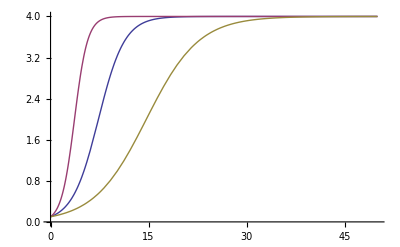

```mathematica
Plot[Evaluate[y[x]/.sol/.{
{a->0.1,r->1/2,K-> 4},{a->0.1,r->1,K-> 4},{a->0.1,r->0.25,K-> 4}}
],{x,0,50}]
```

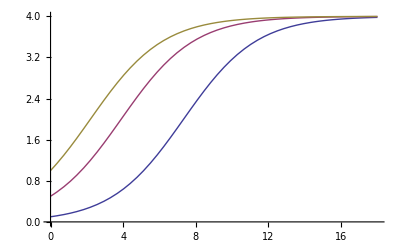

```mathematica
Plot[Evaluate[y[x]/.sol/.{
{a->0.1,r->1/2,K-> 4},{a->0.5,r->1/2,K-> 4},{a->1,r->1/2,K-> 4}}
],{x,0,18}]
```

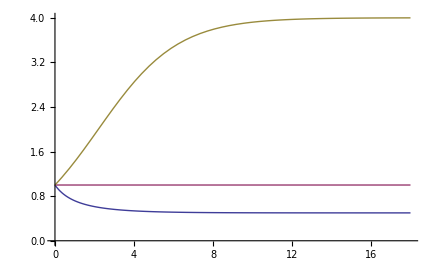

```mathematica
Plot[Evaluate[y[x]/.sol/.{
{a->1,r->1/2,K-> 0.5},{a->1,r->1/2,K-> 1},{a->1,r->1/2,K-> 4}}
],{x,0,18}]
```

```mathematica
solut[a_,r_,K_]:= DSolve[{y'[x] ==r y[x](1-y[x]/K),y[0]==a},y,x]//Quiet
```

```mathematica
ssolut[a_,r_,K_]:=Evaluate[y[x]/.DSolve[{y'[x] ==r y[x](1-y[x]/K),y[0]==a},y,x]//Quiet]
```

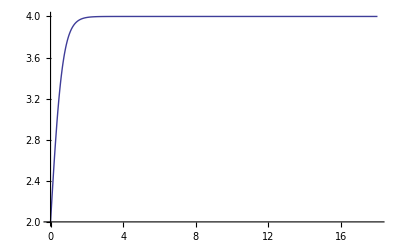

```mathematica
Plot[ssolut[2,3,4],{x,0,18},PlotRange->All]
```

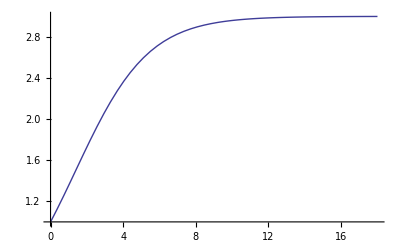

```mathematica
Plot[Evaluate[y[x]/.solut[1,1/2,3]
],{x,0,18}]
```

```mathematica
Hill model
```

```mathematica
Integrate[(1-(y^a)/K)/(r*(y^a)),y,Assumptions->r>0  && K>0 &&a>0]
```

```mathematica
a=2;r=1;K=6
```

```mathematica
ContourPlot[-(y-(K y^(1-a))/(1-a))/(K r)==x,{x,0.1,5},{y,0.1,5}]
```

```mathematica
Plot[Evaluate[-y/(6 2)+Log[y]/2],{y,1,20}]
```

```mathematica
sol= DSolve[{y'[x] ==r*y[x]/(1-y[x]/K),y[0]==a},y,x]//Quiet
```

```mathematica
Plot[Evaluate[x[t]/.sol/.{a->0.01,r-> 2, K->2}],
{t,0,3}]
```

```mathematica
Plot[Evaluate[y[x]/. %
],{x,0,1000}]
```

```mathematica
solut[a_,c_]:=NDSolve[{y'[x] ==a y[x]/(1+y[x]/c),y[0]==0.01},y,{x,0,100}]
```

```mathematica
NDSolve[{y'[x] ==(y[x]^2)(1-(y[x]^2)/3),y[0]==0.01},y,{x,0,1000}]
```

```mathematica
solut[a_,b_,c_]:=NDSolve[{y'[x] ==a (y[x])/(1+(y[x])/c),y[0]==b},y,{x,0,100}]
```

```mathematica
Plot[Evaluate[y[x]/.solut[3,3]],{x,0,100},PlotRange->All]
```

```mathematica
Show[Plot[Evaluate[y[x]/.solut[3,1.2,-3]],{x,0,100},PlotRange->All],Plot[Evaluate[y[x]/.solut[3,1,-1/3]],{x,0,100},PlotRange->All,PlotStyle->Red]]
```

```mathematica
Bernoulli model
```

```mathematica
sol= NDSolve[{y'[x] ==1/2 y[x](1-y[x]^2),y[0]==0.01},y,{x,0,30}]//Quiet
```

{{y→InterpolatingFunction[{{0.,30.}},<>]}}

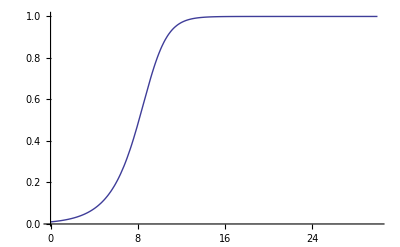

```mathematica
Plot[Evaluate[y[x]/.sol],{x,0,30},PlotRange->All]
```

```mathematica
solut[θ_]:=NDSolve[{y'[x] ==y[x](1-y[x]^θ),y[0]==0.01},y,{x,0,30}]
```

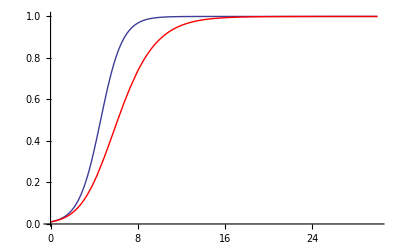

```mathematica
Show[Plot[Evaluate[y[x]/.solut[1]],{x,0,30},PlotRange->All],Plot[Evaluate[y[x]/.solut[1/2]],{x,0,30},PlotRange->All,PlotStyle->Red]]
```

```mathematica
Beverton-Holt model
```

```mathematica
DSolve[y'[x] ==y[x]*b/(1+a y[x])-y[x]*m,y[x],x]
```

{{y[x]→InverseFunction[(-m Log[#1]+b Log[b-m (1+a #1)])/((b-m) m)&][-x+C[1]]}}

```mathematica
solut[a_,b_,m_]:=NDSolve[{y'[x] ==y[x]*b/(1+a y[x])-y[x]*m,y[0]==0.01},y,{x,0,30}]
```

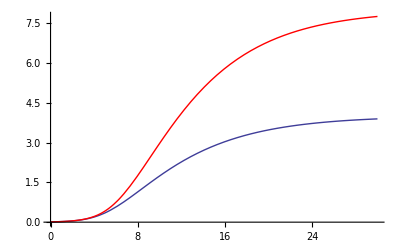

```mathematica
Show[Plot[Evaluate[y[x]/.solut[1,1,0.2]],{x,0,30},PlotRange->All],Plot[Evaluate[y[x]/.solut[1/2,1,0.2]],{x,0,30},PlotRange->All,PlotStyle->Red]]
```

```mathematica
solut[a_]:=NDSolve[{y'[x] ==y[x](1-y[x])/(1+a y[x]),y[0]==0.01},y,{x,0,30}]
```

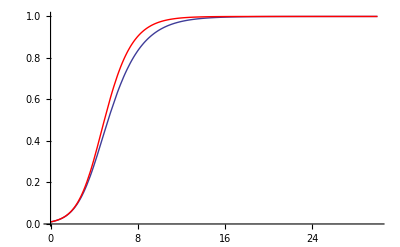

```mathematica
Show[Plot[Evaluate[y[x]/.solut[1]],{x,0,30},PlotRange->All],Plot[Evaluate[y[x]/.solut[1/2]],{x,0,30},PlotRange->All,PlotStyle->Red]]
```

```mathematica
Ricker model
```

```mathematica
solut[g_]:=NDSolve[{y'[x] ==y[x](Exp[g (1-y[x])]-1)/(Exp[g] -1),y[0]==0.01},y,{x,0,30}]
```

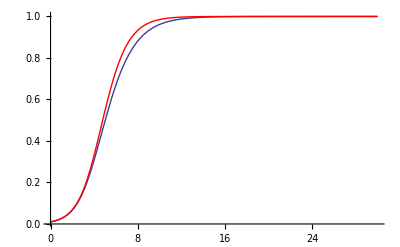

```mathematica
Show[Plot[Evaluate[y[x]/.solut[1]],{x,0,30},PlotRange->All],Plot[Evaluate[y[x]/.solut[1/2]],{x,0,30},PlotRange->All,PlotStyle->Red]]
```

```mathematica
Gompertz model
```

```mathematica
solut=NDSolve[{y'[x] ==-y[x]Log[y[x]],y[0]==0.01},y,{x,0,30}]
```

{{y→InterpolatingFunction[{{0.,30.}},<>]}}

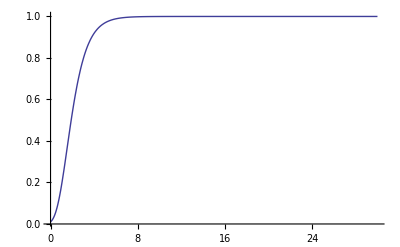

```mathematica
Plot[Evaluate[y[x]/.solut],{x,0,30},PlotRange->All]
```

```mathematica
Monod model
```

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
solut[s0_,x0_,Y_,μm_,K_]=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}]
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

NDSolve[{x'[t]==(μm x[t] (s0-(-x0+x[t])/Y))/(K+s0-(-x0+x[t])/Y),x[0]==x0},x[t],{t,0,50}]

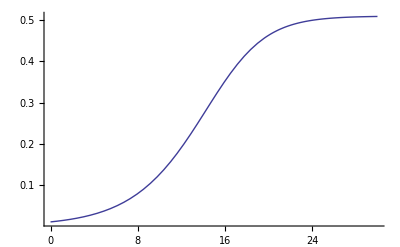

```mathematica
Plot[Evaluate[x[t]/.solut[1,0.01,0.5,0.8,2]],{t,0,30},PlotRange->All]
```

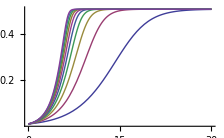

```mathematica
Plot[Evaluate[Table[x[t]/.solut[1,0.01,0.5,0.8,2/c],{c,1,10}]],{t,0,30},PlotRange->All]
```

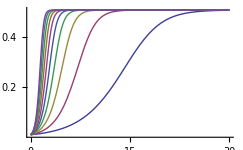

```mathematica
Plot[Evaluate[Table[x[t]/.solut[1,0.01,0.5,0.8*c,2],{c,1,10}]],{t,0,30},PlotRange->All]
```

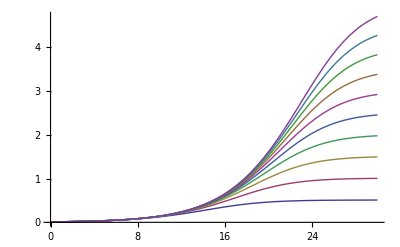

```mathematica
Plot[Evaluate[Table[x[t]/.solut[1,0.01,0.5*c,0.8,2],{c,1,10}]],{t,0,30},PlotRange->All]
```

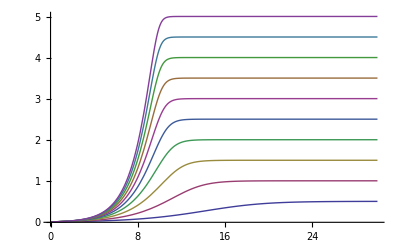

```mathematica
Plot[Evaluate[Table[x[t]/.solut[1*c,0.01,0.5,0.8,2],{c,1,10}]],{t,0,30},PlotRange->All]
```

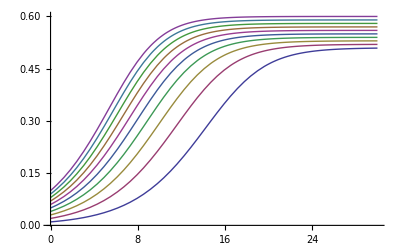

```mathematica
Plot[Evaluate[Table[x[t]/.solut[1,0.01*c,0.5,0.8,2],{c,1,10}]],{t,0,30},PlotRange->All]
```

```mathematica
Data generation for the Monod model
```

```mathematica
x0=0.1;
s0=1;
μm=0.2;
K=0.5;
Y=0.3;
```

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
solut=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

```mathematica
Design=Table[i,{i,2.5,25,2.5}]
```

{2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.}

```mathematica
skl[t_]=Evaluate [x[t]/.solut]
```

{InterpolatingFunction[{{0.,50.}},<>][t]}

```mathematica
Data=skl[Design][[1]]
```

{0.138558,0.188199,0.247523,0.309166,0.358707,0.385786,0.395881,0.398884,0.399704,0.399922}

```mathematica
ErrorF[aa_]=NormalDistribution[aa,0.05]
```

NormalDistribution[aa,0.05]

```mathematica
Data1= Map[RandomReal,Map[ErrorF,Data]]
```

{0.147448,0.190069,0.21553,0.241554,0.237715,0.324921,0.373749,0.364512,0.325268,0.306634}

```mathematica
Data2=Table[{Design[[i]],Data1[[i]]},{i,1,10}]
```

{{2.5,0.147448},{5.,0.190069},{7.5,0.21553},{10.,0.241554},{12.5,0.237715},{15.,0.324921},{17.5,0.373749},{20.,0.364512},{22.5,0.325268},{25.,0.306634}}

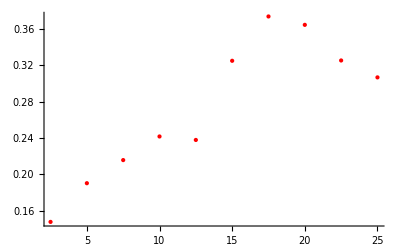

```mathematica
Pl1=ListPlot[Data2,PlotStyle->Red]
```

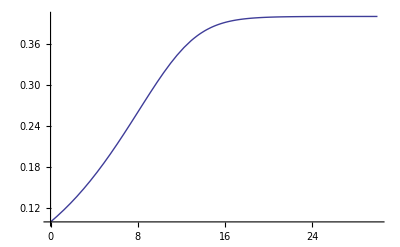

```mathematica
Pl2=Plot[Evaluate[x[t]/.solut],{t,0,30},PlotRange->All]
```

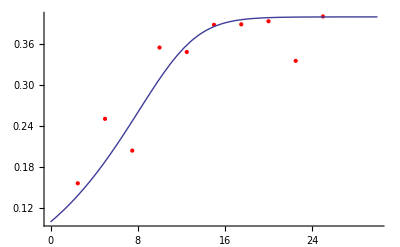

```mathematica
Show[Pl1,Pl2,PlotRange->All]
```

```mathematica
Regression for the Monod model
```

```mathematica
x0=0.1;
s0=1;
```

```mathematica
Design=Table[i,{i,2.5,25,2.5}]
```

{2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.}

```mathematica
ExpData={0.15646348897716994,0.25080538338487457,0.20431975608057,0.3551568894893287,0.3486496271169831,0.38837584954898186,0.3891300856222601,0.39367304553774723,0.3356889370152781,0.4006470549522902}
```

{0.156463,0.250805,0.20432,0.355157,0.34865,0.388376,0.38913,0.393673,0.335689,0.400647}

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
M=100;
```

```mathematica
Do[Θ ={RandomReal[{0.001,1}],RandomReal[{0.001,1}],RandomReal[{0.001,1}]};
μm =Θ [[1]];K=Θ [[2]];Y=Θ [[3]];
solut=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}];
skl[t_]=Evaluate [x[t]/.solut];
Data=skl[Design][[1]] ;
L=Total[#^2&/@(Data-ExpData)];
If[L<M,{M=L,Θ1=Θ}],{n,50000}]
```

```mathematica
M
```

0.0104614

```mathematica
Θ1
```

{0.309627,0.916746,0.283287}

```mathematica
While[M>0.0002,
Θ ={RandomReal[{0.001,1}],RandomReal[{0.001,1}],RandomReal[{0.001,1}]};
μm =Θ [[1]];K=Θ [[2]];Y=Θ [[3]];
solut=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}];
skl[t_]=Evaluate [x[t]/.solut];
Data=skl[Design][[1]] ;
L=Total[#^2&/@(Data-ExpData)];
If[L<M,{M=L,Θ1=Θ}]]
```

```mathematica
M
```

0.000245629

```mathematica
Θ1
```

{0.184465,0.44018,0.292206}

```mathematica
Pl2=Plot[Evaluate[x[t]/.solut],{t,0,30},PlotRange->All]
```

```mathematica
Regression for the Monod model 2
```

```mathematica
x0=0.1;
s0=1;
```

```mathematica
Design=Table[i,{i,2.5,25,2.5}]
```

{2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.}

```mathematica
ExpData={0.15646348897716994,0.25080538338487457,0.20431975608057,0.3551568894893287,0.3486496271169831,0.38837584954898186,0.3891300856222601,0.39367304553774723,0.3356889370152781,0.4006470549522902}
```

{0.156463,0.250805,0.20432,0.355157,0.34865,0.388376,0.38913,0.393673,0.335689,0.400647}

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
M=100;
```

```mathematica
Do[Θ ={RandomReal[{0.001,1}],RandomReal[{0.001,1}],RandomReal[{0.001,1}]};
μm =Θ [[1]];K=Θ [[2]];Y=Θ [[3]];
solut=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}];
skl[t_]=Evaluate [x[t]/.solut];
Data=skl[Design][[1]] ;
L=Total[#^2&/@(Data-ExpData)];
If[L<M,{M=L,Θ1=Θ}],{n,50000}]
```

```mathematica
M
```

0.0104614

```mathematica
Θ1
```

{0.309627,0.916746,0.283287}

```mathematica
M
```

0.0103959

```mathematica
Θ1
```

{0.26437,0.708347,0.281431}

```mathematica
M
```

0.0104894

```mathematica
Θ1
```

{0.180822,0.292752,0.27879}

```mathematica
Plot Pl1
```

```mathematica
Data2={{2.5,0.15646348897716994},{5.,0.25080538338487457},{7.5,0.20431975608057},{10.,0.3551568894893287},{12.5,0.3486496271169831},{15.,0.38837584954898186},{17.5,0.3891300856222601},{20.,0.39367304553774723},{22.5,0.3356889370152781},{25.,0.4006470549522902}}
```

{{2.5,0.156463},{5.,0.250805},{7.5,0.20432},{10.,0.355157},{12.5,0.34865},{15.,0.388376},{17.5,0.38913},{20.,0.393673},{22.5,0.335689},{25.,0.400647}}

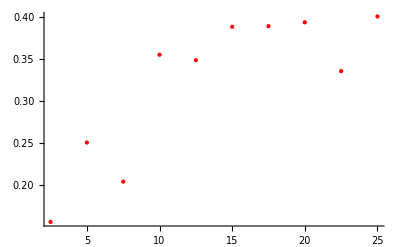

```mathematica
Pl1=ListPlot[Data2,PlotStyle->Red]
```

```mathematica
Plot Pl5
```

```mathematica
x0=0.1;
s0=1;
μm=0.2;
K=0.5;
Y=0.3;
```

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
solut5=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

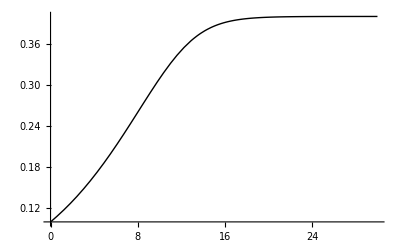

```mathematica
Pl5=Plot[Evaluate[x[t]/.solut5],{t,0,30},PlotRange->All,PlotStyle->Black]
```

```mathematica
Plot Pl4
```

```mathematica
x0=0.1;
s0=1;
μm=0.18082230867991034;
K=0.2927523903608605;
Y=0.2787896671609218;
```

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
solut2=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

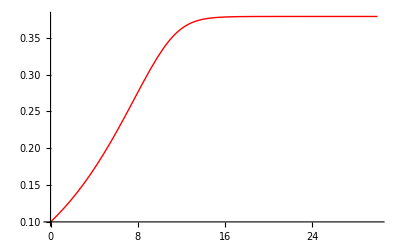

```mathematica
Pl4=Plot[Evaluate[x[t]/.solut2],{t,0,30},PlotRange->All,PlotStyle->Red]
```

```mathematica
Plot Pl3
```

```mathematica
x0=0.1;
s0=1;
μm=0.2643704450264549;
K=0.7083468588940259;
Y=0.28143097414565404;
```

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
solut1=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

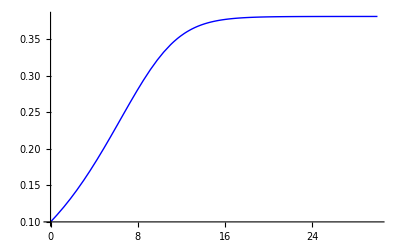

```mathematica
Pl3=Plot[Evaluate[x[t]/.solut1],{t,0,30},PlotRange->All,PlotStyle->Blue]
```

```mathematica
Plot Pl2
```

```mathematica
x0=0.1;
s0=1;
μm=0.3096270483422572;
K=0.9167462919552626;
Y=0.2832869647588717;
```

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
solut=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

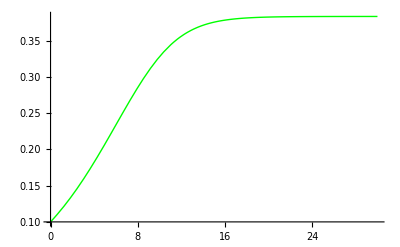

```mathematica
Pl2=Plot[Evaluate[x[t]/.solut],{t,0,30},PlotRange->All,PlotStyle->Green]
```

```mathematica
Final plot
```

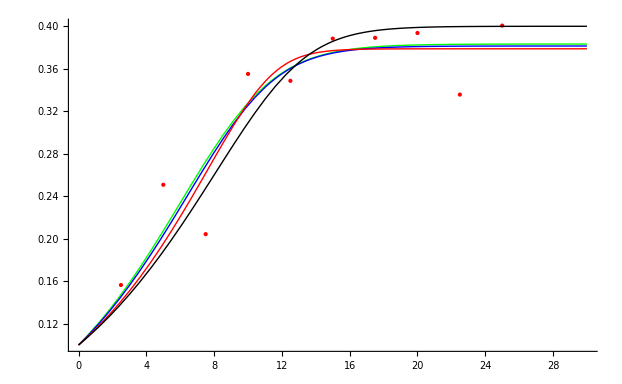

```mathematica
Show[Pl1,Pl2,Pl3,Pl4,Pl5,PlotRange->All]
```

```mathematica
Regression for the Monod model - correlation of estimates
```

```mathematica
x0=0.1;
s0=1;
```

```mathematica
Design=Table[i,{i,2.5,25,2.5}]
```

{2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.}

```mathematica
ExpData={0.15646348897716994,0.25080538338487457,0.20431975608057,0.3551568894893287,0.3486496271169831,0.38837584954898186,0.3891300856222601,0.39367304553774723,0.3356889370152781,0.4006470549522902}
```

{0.156463,0.250805,0.20432,0.355157,0.34865,0.388376,0.38913,0.393673,0.335689,0.400647}

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
Distances={};
MuEstimates={};
KEstimates={};
YEstimates={};
```

```mathematica
Do[
M=100;
Do[Θ ={RandomReal[{0.001,1}],RandomReal[{0.001,1}],RandomReal[{0.001,1}]};
μm =Θ [[1]];K=Θ [[2]];Y=Θ [[3]];
solut=NDSolve[{x'[t]==μ[s[x[t]]] x[t], x[0]==x0},x[t],{t,0,50}];
skl[t_]=Evaluate [x[t]/.solut];
Data=skl[Design][[1]] ;
L=Total[#^2&/@(Data-ExpData)];
If[L<M,{M=L,Θ1=Θ}],{n,10000}];
Distances=AppendTo[Distances,M];
MuEstimates=AppendTo[MuEstimates,Θ1[[1]]];
KEstimates=AppendTo[KEstimates,Θ1[[2]]];
YEstimates=AppendTo[YEstimates,Θ1[[3]]]
,{m,4}]
```

```mathematica
Distances
```

{0.0105088,0.0104205,0.0104944,0.0104105}

```mathematica
MuEstimates
```

{0.18866,0.305849,0.20864,0.243108}

```mathematica
KEstimates
```

{0.314907,0.948513,0.407512,0.619888}

```mathematica
YEstimates
```

{0.279459,0.283057,0.279366,0.284521}

```mathematica
MuAverageEst=Mean[MuEstimates]
```

0.236564

```mathematica
KAverageEst=Mean[KEstimates]
```

0.572705

```mathematica
YAverageEst=Mean[YEstimates]
```

0.281601

```mathematica
Correlation[MuEstimates,KEstimates]
```

0.999341

```mathematica
Correlation[MuEstimates,YEstimates]
```

0.712093

```mathematica
Correlation[KEstimates,YEstimates]
```

0.733268

```mathematica
Optimal experimental design for the Monod model
```

```mathematica
Design=Table[i,{i,2.5,25,2.5}]
```

{2.5,5.,7.5,10.,12.5,15.,17.5,20.,22.5,25.}

```mathematica
s[x_]:=s0- (x-x0)/Y
```

```mathematica
μ[s_]:=μm s/(K+s)
```

```mathematica
∫1/(μ[s[x]] x)ⅆx
```

-(-(x0+(K+s0) Y) Log[x]+K Y Log[x-x0-s0 Y])/((x0+s0 Y) μm)

```mathematica
F[ μm_,K_,Y_,t_,x_]:=(-(x0+(K+s0) Y) Log[x]+K Y Log[x-x0-s0 Y])/((x0+s0 Y) μm)+t
```

```mathematica
-D[F[ μm,K,Y,t,x],μm]/D[F[ μm,K,Y,t,x],x]
```

((-x0-(K+s0) Y) Log[x]+K Y Log[x-x0-s0 Y])/(((K Y)/(x-x0-s0 Y)+(-x0-(K+s0) Y)/x) μm)

```mathematica
-D[F[ μm,K,Y,t,x],K]/D[F[ μm,K,Y,t,x],x]
```

-(-Y Log[x]+Y Log[x-x0-s0 Y])/((K Y)/(x-x0-s0 Y)+(-x0-(K+s0) Y)/x)

```mathematica
-D[F[ μm,K,Y,t,x],Y]/D[F[ μm,K,Y,t,x],x]
```

((x0+s0 Y) μm (-(-(K s0 Y)/(x-x0-s0 Y)+(-K-s0) Log[x]+K Log[x-x0-s0 Y])/((x0+s0 Y) μm)+(s0 ((-x0-(K+s0) Y) Log[x]+K Y Log[x-x0-s0 Y]))/((x0+s0 Y)^2 μm)))/((K Y)/(x-x0-s0 Y)+(-x0-(K+s0) Y)/x)

```mathematica
Fm[ μm_,K_,Y_,t_,x_]:=((-x0-(K+s0) Y) Log[x]+K Y Log[x-x0-s0 Y])/(((K Y)/(x-x0-s0 Y)+(-x0-(K+s0) Y)/x) μm)
```

```mathematica
FK[ μm_,K_,Y_,t_,x_]:=-(-Y Log[x]+Y Log[x-x0-s0 Y])/((K Y)/(x-x0-s0 Y)+(-x0-(K+s0) Y)/x)
```

```mathematica
FY[ μm_,K_,Y_,t_,x_]:=((x0+s0 Y) μm (-(-(K s0 Y)/(x-x0-s0 Y)+(-K-s0) Log[x]+K Log[x-x0-s0 Y])/((x0+s0 Y) μm)+(s0 ((-x0-(K+s0) Y) Log[x]+K Y Log[x-x0-s0 Y]))/((x0+s0 Y)^2 μm)))/((K Y)/(x-x0-s0 Y)+(-x0-(K+s0) Y)/x)
```

```mathematica
FisherMatrix[ μm_,K_,Y_,t_,x_]:=({{Fm[ μm,K,Y,t,x].Fm[ μm,K,Y,t,x], Fm[ μm,K,Y,t,x].FK[ μm,K,Y,t,x], Fm[ μm,K,Y,t,x].FY[ μm,K,Y,t,x]}, {FK[ μm,K,Y,t,x].Fm[ μm,K,Y,t,x], FK[ μm,K,Y,t,x].FK[ μm,K,Y,t,x], FK[ μm,K,Y,t,x].FY[ μm,K,Y,t,x]}, {FY[ μm,K,Y,t,x].Fm[ μm,K,Y,t,x], FY[ μm,K,Y,t,x].FK[ μm,K,Y,t,x], FY[ μm,K,Y,t,x].FY[ μm,K,Y,t,x]}})
```

```mathematica
x0=0.1;
s0=1;
```

```mathematica
N[FisherMatrix[0.2,0.5,0.3,Design,Design]]
```

{{535369.,-593.541,-999.179},{-593.541,0.986517,1.67819},{-999.179,1.67819,2.8559}}

```mathematica
Pl2=Plot[Evaluate[x[t]/.solut],{t,0,30},PlotRange->All]
```

```mathematica
Predator-Prey Model - Local Stability Analysis
```

```mathematica
f[x_,y_]:=x-x y;
g[x_,y_]:=x y - α y;
```

```mathematica
J[x_,y_]=({{D[f[x,y], x], D[f[x,y], y]}, {D[g[x,y], x], D[g[x,y], y]}})
```

{{1-y,-x},{y,x-α}}

```mathematica
Stationarystates={x,y}/.Solve[f[x,y]==0&&g[x,y]==0,{x,y}]
```

{{α,1},{0,0}}

```mathematica
Stattionary state {0, 0}
```

```mathematica
J1=J[Stationarystates[[2,1]],Stationarystates[[2,2]]]
```

{{1,0},{0,-α}}

```mathematica
Equation1=(x'[t]==(J1.{x[t],y[t]})[[1]])
```

x'[t]==x[t]

```mathematica
Equation2=(y'[t]==(J1.{x[t],y[t]})[[2]])
```

y'[t]==-α y[t]

```mathematica
State1=DSolve[{Equation1,Equation2,x[0]==a,y[0]==b},{x,y}, t]
```

{{x→Function[{t},a ⅇ^t],y→Function[{t},b ⅇ^(-t α)]}}

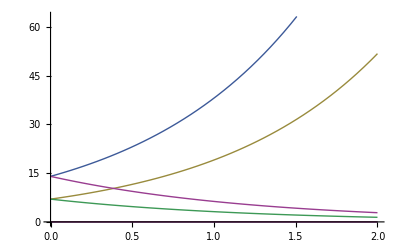

```mathematica
Plot[Table[{x[t], y[t]}/.State1/.{a->m, b->m,α->0.8}, {m,0,20,7}], {t,0,2},Evaluated->True]
```

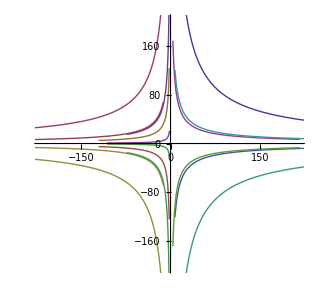

```mathematica
ParametricPlot[Table[{x[t], y[t]}/.State1/.{a->3 m Sin[m], b->3 m Cos[m],α->0.8}, {m,-40,40,5}], {t,-2,2},Evaluated->True]
```

```mathematica
Stattionary state {α, 1}
```

```mathematica
J2=J[Stationarystates[[1,1]],Stationarystates[[1,2]]]
```

{{0,-α},{1,0}}

```mathematica
Equation1a=(x'[t]==(J2.{x[t],y[t]})[[1]])
```

x'[t]==-α y[t]

```mathematica
Equation2a=(y'[t]==(J2.{x[t],y[t]})[[2]])
```

y'[t]==x[t]

```mathematica
State2=DSolve[{Equation1a,Equation2a,x[0]==a,y[0]==b},{x,y}, t]
```

{{x→Function[{t},a Cos[t √α]-b √α Sin[t √α]],y→Function[{t},(b √α Cos[t √α]+a Sin[t √α])/(√α)]}}

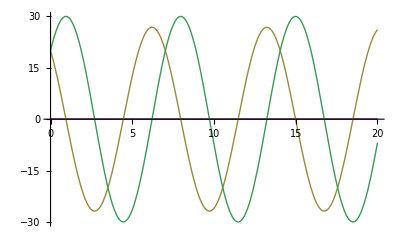

```mathematica
Plot[Table[{x[t], y[t]}/.State2/.{a->m, b->m,α->0.8}, {m,0,20,20}], {t,0,20},Evaluated->True]
```

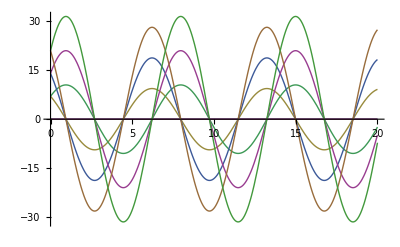

```mathematica
Plot[Table[{x[t], y[t]}/.State2/.{a->m, b->m,α->0.8}, {m,0,25,7}], {t,0,20},Evaluated->True]
```

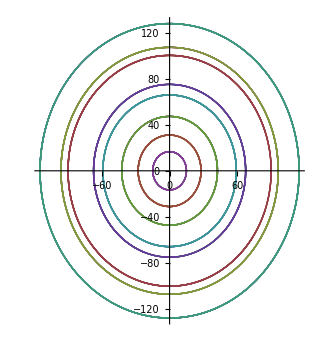

```mathematica
ParametricPlot[Table[{x[t], y[t]}/.State2/.{a->3 m Sin[m], b->3 m Cos[m],α->0.8}, {m,-40,40,5}], {t,-10,10},Evaluated->True]
```

```mathematica
Predator-Prey Model - Numerical Analysis of the Nonlinear System
```

```mathematica
f[x_,y_]:=x-x y;
g[x_,y_, α_]:=x y - α y;
```

```mathematica
Equation1=(x'[t]==f[x[t],y[t]])
```

x'[t]==x[t]-x[t] y[t]

```mathematica
Equation2[ α_]=(y'[t]==g[x[t],y[t], α])
```

y'[t]==-α y[t]+x[t] y[t]

```mathematica
PPSolution[a_,b_, α_]:=NDSolve[{Equation1,Equation2[α],x[0]==a,y[0]==b},{x,y},{t,0, 30}]
```

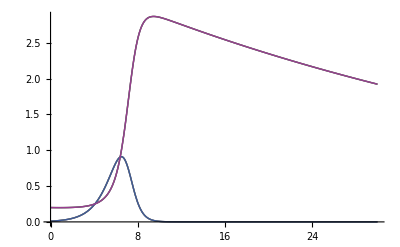

```mathematica
Plot[Table[{x[t], y[t]}/.PPSolution[0.01,0.2,0.02], {m,0,20,7}], {t,0,30},Evaluated->True]
```

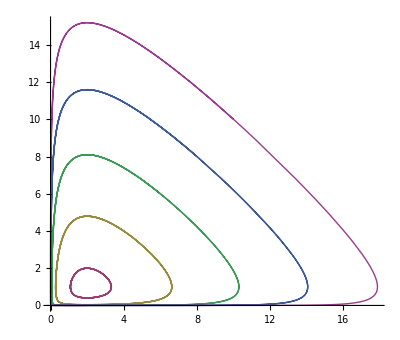

```mathematica
ParametricPlot[Table[{x[t], y[t]}/.PPSolution[m,m,2],{m,0,10,2}], {t,0,20},Evaluated->True,AxesOrigin->{0,0},PlotRange->All]
```

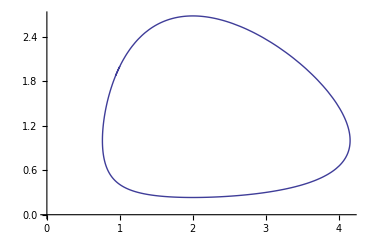

```mathematica
ParametricPlot[{x[t], y[t]}/.PPSolution[1,2,2], {t,0,4.9},Evaluated->True,AxesOrigin->{0,0}]
```

```mathematica
Dicrete models
```

```mathematica
RSolve[x[n+1]-x[n]-x[n-1]==0,x[n], n]
```

{{x[n]→C[1] Fibonacci[n]+C[2] LucasL[n]}}

```mathematica
RSolve[{x[n+1]-x[n]-x[n-1]==0,x[0]==1,x[1]==1},x[n],n]
```

{{x[n]→1/2 (Fibonacci[n]+LucasL[n])}}

```mathematica
A=({{0, 1}, {1, 1}})
```

{{0,1},{1,1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1+√5),1/2 (1-√5)}

```mathematica
Tr[A]
```

1

```mathematica
Det[A]
```

-1

```mathematica
SIR model
```

```mathematica
f[x_,y_]:=x y;
g[x_,y_]:=x y - y;
```

```mathematica
Equation1=(x'[t]==-f[x[t],y[t]])
```

x'[t]==-x[t] y[t]

```mathematica
Equation2=(y'[t]==g[x[t],y[t]])
```

y'[t]==-y[t]+x[t] y[t]

```mathematica
Equation3=(z'[t]==y[t])
```

z'[t]==y[t]

```mathematica
PPSolution[a_,b_]:=NDSolve[{Equation1,Equation2,x[0]==a,y[0]==b},{x,y},{t,0, 30}]
```

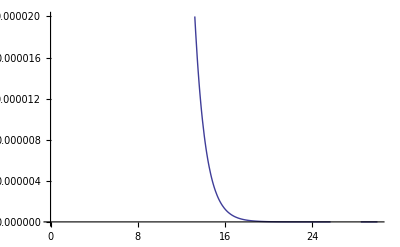

```mathematica
Plot[y[t]/.PPSolution[0.2,11], {t,0,30},Evaluated->True,PlotRange->{0,0.00002}]
```

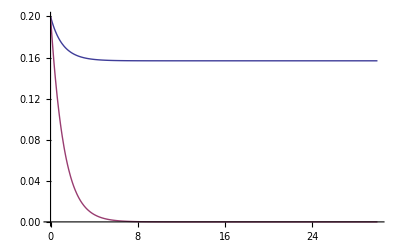

```mathematica
Plot[{x[t], y[t]}/.PPSolution[0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

```mathematica
PPSolution3[a_,b_,c_]:=NDSolve[{Equation1,Equation2,Equation3,x[0]==a,y[0]==b,z[0]==c},{x,y,z},{t,0, 30}]
```

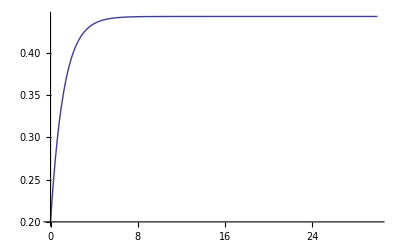

```mathematica
Plot[z[t]/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

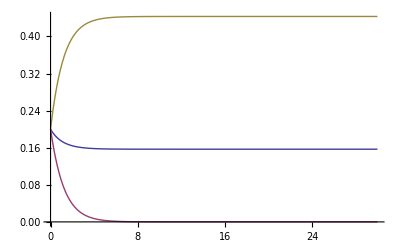

```mathematica
Plot[{x[t], y[t],z[t]}/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

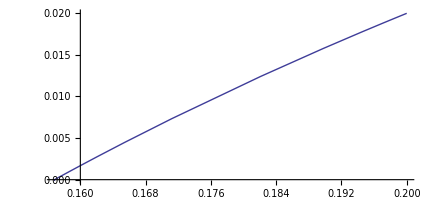

```mathematica
ParametricPlot[{x[t], y[t]/10}/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

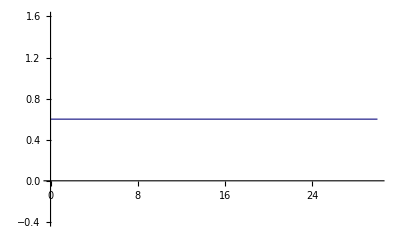

```mathematica
Plot[{x[t]+ y[t]+z[t]}/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
(x[20]/.PPSolution3[0.2,0.2,0.2])[[1]]/0.2*100
```

78.4136

```mathematica
J[x_,y_]=({{-D[f[x,y], x], -D[f[x,y], y]}, {D[g[x,y], x], D[g[x,y], y]}})
```

{{-y,-x},{y,-1+x}}

```mathematica
MatrixForm[J[x,y]]
```

(-y | -x
y | -1+x)

```mathematica
Stationarystates={x,y}/.Solve[f[x,y]==0&&g[x,y]==0,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x,0}}

```mathematica
Stattionary state {x, 0}
```

```mathematica
J1[x_]:=J[x,0]
```

```mathematica
J1[a]
```

{{0,-a},{0,-1+a}}

```mathematica
Equation1=(x'[t]==(J1[a].{x[t],y[t]})[[1]])
```

x'[t]==a y[t]

```mathematica
Equation2=(y'[t]==(J1[a].{x[t],y[t]})[[2]])
```

y'[t]==(-1+a) y[t]

```mathematica
State1=DSolve[{Equation1,Equation2,x[0]==a,y[0]==c},{x,y}, t]
```

{{x→Function[{t},(a (-1+a-c+c ⅇ^((-1+a) t)))/(-1+a)],y→Function[{t},c ⅇ^((-1+a) t)]}}

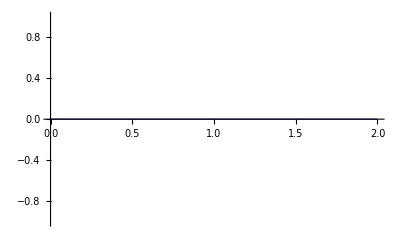

```mathematica
Plot[Table[{x[t], y[t]}/.State1/.{a->m, b->m,α->0.8}, {m,0,20,7}], {t,0,2},Evaluated->True]
```

```mathematica
Reaction advection diffision model
```

```mathematica
DSolve[3D[u[t,x],t]+5D[u[t,x],x]==0 ,u,{t,x}]
```

{{u→Function[{t,x},C[1][1/3 (-5 t+3 x)]]}}

The solution with a particular choice of the arbitrary function C[1]:

```mathematica
(y[x1,x2]/.%[[1]])/.{C[1][e_]:>Sin[e]+Cos[e]}
```

1/6 (x1^2+6 (Cos[1/3 (-5 x1+3 x2)]+Sin[1/3 (-5 x1+3 x2)]))

```mathematica
Plot3D[%,{x1,-5,5},{x2,-5,5}]
```

-Graphics-

```mathematica
f[x_,y_]:=x y;
g[x_,y_]:=x y - y;
```

```mathematica
Equation1=(x'[t]==-f[x[t],y[t]])
```

x'[t]==-x[t] y[t]

```mathematica
Equation2=(y'[t]==g[x[t],y[t]])
```

y'[t]==-y[t]+x[t] y[t]

```mathematica
Equation3=(z'[t]==y[t])
```

z'[t]==y[t]

```mathematica
PPSolution[a_,b_]:=NDSolve[{Equation1,Equation2,x[0]==a,y[0]==b},{x,y},{t,0, 30}]
```

```mathematica
Plot[y[t]/.PPSolution[0.2,11], {t,0,30},Evaluated->True,PlotRange->{0,0.00002}]
```

-Graphics-

```mathematica
Plot[{x[t], y[t]}/.PPSolution[0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

-Graphics-

```mathematica
PPSolution3[a_,b_,c_]:=NDSolve[{Equation1,Equation2,Equation3,x[0]==a,y[0]==b,z[0]==c},{x,y,z},{t,0, 30}]
```

```mathematica
Plot[z[t]/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

-Graphics-

```mathematica
Plot[{x[t], y[t],z[t]}/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

-Graphics-

```mathematica
ParametricPlot[{x[t], y[t]/10}/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All]
```

-Graphics-

```mathematica
Plot[{x[t]+ y[t]+z[t]}/.PPSolution3[0.2,0.2,0.2], {t,0,30},Evaluated->True,PlotRange->All,AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
(x[20]/.PPSolution3[0.2,0.2,0.2])[[1]]/0.2*100
```

78.4136

```mathematica
J[x_,y_]=({{-D[f[x,y], x], -D[f[x,y], y]}, {D[g[x,y], x], D[g[x,y], y]}})
```

{{-y,-x},{y,-1+x}}

```mathematica
MatrixForm[J[x,y]]
```

(-y | -x
y | -1+x)

```mathematica
Stationarystates={x,y}/.Solve[f[x,y]==0&&g[x,y]==0,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x,0}}

```mathematica
Stattionary state {x, 0}
```

```mathematica
J1[x_]:=J[x,0]
```

```mathematica
J1[a]
```

{{0,-a},{0,-1+a}}

```mathematica
Equation1=(x'[t]==(J1[a].{x[t],y[t]})[[1]])
```

x'[t]==a y[t]

```mathematica
Equation2=(y'[t]==(J1[a].{x[t],y[t]})[[2]])
```

y'[t]==(-1+a) y[t]

```mathematica
State1=DSolve[{Equation1,Equation2,x[0]==a,y[0]==c},{x,y}, t]
```

{{x→Function[{t},(a (-1+a-c+c ⅇ^((-1+a) t)))/(-1+a)],y→Function[{t},c ⅇ^((-1+a) t)]}}

```mathematica
Plot[Table[{x[t], y[t]}/.State1/.{a->m, b->m,α->0.8}, {m,0,20,7}], {t,0,2},Evaluated->True]
```

-Graphics-